### Definiciones

```mathematica
prod=KroneckerProduct;
mf=MatrixForm;
fs=FullSimplify;

(*Estados de un qubit*)
b1[0]={1,0}(*estado 0, ground state, o spin up*);
b1[1]={0,1}(*estado 1, excited state, o spin down*);

(*Estados de dos qubits*)
Clear[e]
(*sin el flatten da una matriz*)
e[1]=Flatten[KroneckerProduct[b1[0],b1[0]]] 
e[2]=Flatten[KroneckerProduct[b1[0],b1[1]]]
e[3]=Flatten[KroneckerProduct[b1[1],b1[0]]]
e[4]=Flatten[KroneckerProduct[b1[1],b1[1]]]
```

{1,0,0,0}

{0,1,0,0}

{0,0,1,0}

{0,0,0,1}

### Problema I-3. b)

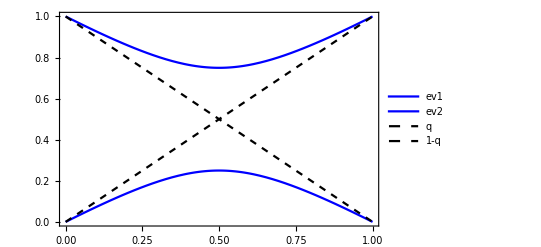

```mathematica
ρ={{Cos[θ]^2,(-1+2q)Cos[θ]Sin[θ]},{(-1+2q)Cos[θ]Sin[θ],Sin[θ]^2}};
ev=Eigenvalues[ρ];
Clear[ρ,θ]
θ=π/3;
Plot[{ev[[1]],ev[[2]],q,1-q},{q,0,1},
Frame->True,
PlotStyle->{Blue,Blue,{Black,Dashed},{Black,Dashed}},
PlotLegends->{"ev1","ev2","q","1-q"}]
Clear[ev,θ]
```

```mathematica
(*esta rutina calcula la matriz densidad, elemento por elemento en la base 
e[i] definida arriba.*)
dm[ψin_]:=Module[{ψ=ψin,f,ρ,out},
ρ={};
Do[f={};
Do[AppendTo[f,(Conjugate[e[i]].ψ)(Conjugate[ψ].e[j])],{j,1,4}](*filas de ρ*)
AppendTo[ρ,f]
,{i,1,4}];
out=ρ(*output*)
 ]
```

```mathematica
ψa=(e[1]+e[4])/(√2);ψa2=(e[1]-e[4])/(√2);
ψb=(e[2]+e[3])/(√2);ψb2=(e[2]-e[3])/(√2);
ψc=(e[1]+e[2]-e[3]-e[4])/2;
Print[dm[ψa] //mf,dm[ψb]//mf,dm[ψc]//mf]
```

(1/2 | 0 | 0 | 1/2
0 | 0 | 0 | 0
0 | 0 | 0 | 0
1/2 | 0 | 0 | 1/2)(0 | 0 | 0 | 0
0 | 1/2 | 1/2 | 0
0 | 1/2 | 1/2 | 0
0 | 0 | 0 | 0)(1/4 | 1/4 | -1/4 | -1/4
1/4 | 1/4 | -1/4 | -1/4
-1/4 | -1/4 | 1/4 | 1/4
-1/4 | -1/4 | 1/4 | 1/4)

```mathematica
(*Como wolfram no distingue entre vectores filas y columnas; y no hace falta conjugar porque los coeficientes son reales, puede hacerse*)
```

```mathematica
ρa=prod[ψa,ψa];
ρa2=prod[ψa2,ψa2];
(*inciso b*)
ρb=prod[ψb,ψb];
ρb2=prod[ψb,ψb];
(*inciso c*)
ρc=prod[ψc,ψc];
Print[ρa//mf,ρb//mf,ρc//mf]
```

(1/2 | 0 | 0 | 1/2
0 | 0 | 0 | 0
0 | 0 | 0 | 0
1/2 | 0 | 0 | 1/2)(0 | 0 | 0 | 0
0 | 1/2 | 1/2 | 0
0 | 1/2 | 1/2 | 0
0 | 0 | 0 | 0)(1/4 | 1/4 | -1/4 | -1/4
1/4 | 1/4 | -1/4 | -1/4
-1/4 | -1/4 | 1/4 | 1/4
-1/4 | -1/4 | 1/4 | 1/4)

### problema II.2 --Descomposicion de Schmidt (siguiendo el Nielsen)

```mathematica
schmidt[ψin_]:=Module[{ψ=ψin,,u,d,v,iA,jB,psi,a,b,out},
a=Table[0,{i,1,2},{j,1,2}]; (*Inicializo la matriz de coeficientes Subscript[a, ij]*)
b={{1,0},{0,1}};(*vectores base de un qubit*)

(*coeficientes de la expansion de ψ en la base |ij⟩*)
Do[a[[i]][[j]]=Conjugate[Flatten[prod[b[[i]],b[[j]]]]] .ψ,
{i,1,2},{j,1,2}];
(*Print["Rank(a_ij)=",MatrixRank[a]];*)
(*SVD -- atencion a las convenciones para llamar u,v*)
{u,d,v}=SingularValueDecomposition[a];

(*base de Schmidt*)
iA=Transpose[u].Transpose[b] ;
(*las columnas de b1^t son los vectores de la base*)
jB=ConjugateTranspose[v].Transpose[b];

(*chequeo de consistencia*)
psi=Sum[d[[k]][[k]] Flatten[prod[iA[[k]],jB[[k]]]],{k,1,2}];
(*Print["Chequeo: flag ≠ OverVector[0] ⧦ problemas | ","flag=",psi-ψ]*)

;
out={{iA,jB},Diagonal[d]}
]
```

```mathematica
schmidt[ψc]
```

Rank(a_ij)=1

{{{{1/(√2),-1/(√2)},{1/(√2),1/(√2)}},{{1/(√2),1/(√2)},{-1/(√2),1/(√2)}}},{1,0}}

### problema II.3 --Matriz densidad reducida:

```mathematica
(*usando el codigo de Alan, la traza parcial en B se escribe*)
Map[Tr,Partition[ρa,{2,2}],{2}]
```

{{1/2,0},{0,1/2}}

```mathematica
(*Donde, por un lado 'Partition' crea particiones de las matrices en submatrices mas pequeñas*)
Partition[ρa,{2,2}]
Partition[ρa,{2,2}]//mf
```

{{{{1/2,0},{0,0}},{{0,1/2},{0,0}}},{{{0,0},{1/2,0}},{{0,0},{0,1/2}}}}

((1/2 | 0
0 | 0) | (0 | 1/2
0 | 0)
(0 | 0
1/2 | 0) | (0 | 0
0 | 1/2))

```mathematica
(*como calculo la trazaA? no entiendo bien que cuenta hace*)
```

#### Alternativa: codigo de internet. (esta al final del notebook)

```mathematica
ρaA=TraceSystem[ρa,{2}](*Traza parcial B de la matriz ρa *)
ρaB=TraceSystem[ρa,{1}](*Traza parcial A de la matriz ρa *)
ρbA=TraceSystem[ρb,{2}](*Traza parcial B de la matriz ρb *)
ρcA=TraceSystem[ρc,{2}](*Traza parcial B de la matriz ρc *)
```

{{1/2,0},{0,1/2}}

{{1/2,0},{0,1/2}}

{{1/2,0},{0,1/2}}

{{1/2,-1/2},{-1/2,1/2}}

### Entropia de entrelazamiento :

```mathematica
(*Por definicion, S(ρ)=-Tr[ρ Log[ρ]]*)

(*como entrada, la funcion entropy toma los autovalores del operador densidad*)
entropy[evlist_]:=Module[{ev=evlist,x={},S},
Do[
If[ev[[i]]≠0, 
AppendTo[x,ev[[i]]Log2[ev[[i]]]] 
]
,{i,1,Length[ev]}];
S=-Sum[x[[j]],{j,1,Length[x]}]
 ]
```

```mathematica
Print["S(ρa)=",entropy[Eigenvalues[ρa]]]
Print["S(ρaA)=",entropy[Eigenvalues[ρaA]]]
Print["S(ρb)=",entropy[Eigenvalues[ρb]]]
Print["S(ρbA)=",entropy[Eigenvalues[ρbA]]]
Print["S(ρc)=",entropy[Eigenvalues[ρc]]]
Print["S(ρcA)=",entropy[Eigenvalues[ρcA]]]
```

S(ρa)=0

S(ρaA)=1

S(ρb)=0

S(ρbA)=1

S(ρc)=0

S(ρcA)=0

### problema II.4

```mathematica
Clear[ψ];
ψ=α (e[1]+e[4])/(√2)+ β (e[2]+e[3])/(√2);

(*primero, para saber si este estado puro es producto (separable) o entrelazado, 
calculo la matriz de coeficientes:*)
Clear[a,b];
a=Table[0,{i,1,2},{j,1,2}]; (*Inicializo la matriz de coeficientes Subscript[a, ij]*)
b={{1,0},{0,1}};(*vectores base de un qubit*)

(*coeficientes de la expansion de ψ en la base |ij⟩*)
Do[a[[i]][[j]]=Conjugate[Flatten[prod[b[[i]],b[[j]]]]] .ψ,
{i,1,2},{j,1,2}];
Print["C=",a//mf," |  Det(C)=",Det[a]]
Clear[a,b]
```

C=(α/(√2) | β/(√2)
β/(√2) | α/(√2)) |  Det(C)=α^2/2-β^2/2

```mathematica
(*Tiene determinante nulo, o sea rango 1 cuando |α|=|β|, en ese caso el estado es producto*)
```

```mathematica
(*calculo su matriz densidad, la traza parcial y la entropia de entrelazamiento de un qubit*)
TraceSystem[dm[ψ/.β-> √(1-α^2)/. { α-> 1}],{2}];
ev=Eigenvalues[%]
entropy[ev](*la rutina entropy solo anda bien con valores numericos, no simbolicos*)
```

{1/2,1/2}

1

```mathematica
Usando la descomposicion de Schmidt
```

```mathematica
(*en la DVS, se obtienen los autovalores de la matriz densidad.*)
schmidt[ψ];
(*me dan distintos que con el metodo normal...
aunque obtengo la misma entropia.
*)
```

```mathematica
ev={(1-2Re[α Conjugate[β]])/2,(1+2Re[α Conjugate[β]])/2};
(*veo que cuando α o β valen 0, los dos autovalores son iguales, maxima incerteza
cuando |α|=|β| uno puede anular el primer o el segundo autovalor, dando maxima certeza
*)
entropy[ev/.β-> √(1-α^2)/. { α-> 0.8}]
(*por que aca no hace falta calcular ninguna traza parcial?*)
```

0.141441

### Base de Bell

```mathematica
Clear[B]
B[1]=Flatten[(prod[b1[0],b1[0]]+prod[b1[1],b1[1]])/(√2)];
B[2]=Flatten[(prod[b1[0],b1[0]]-prod[b1[1],b1[1]])/(√2)];
B[3]=Flatten[(prod[b1[0],b1[1]]+prod[b1[1],b1[0]])/(√2)];
B[4]=Flatten[(prod[b1[0],b1[1]]-prod[b1[1],b1[0]])/(√2)];
sz={{1,0},{0,-1}};sp={{0,1},{0,0}};sm=Transpose[sp];sx=(sp+sm);
sy=(sp-sm)/(I);
s1[1]=sx;
s1[2]=sy;
s1[3]=sz;s1[0]={{1,0},{0,1}};
```

```mathematica
xx=prod[sx,sx];
yy=prod[sy,sy];
zz=prod[sz,sz];
```

```mathematica
M={B[1],B[2],B[3],B[4]};
Print[M.xx.ConjugateTranspose[M]//mf,
M.yy.ConjugateTranspose[M]//mf,
M.zz.ConjugateTranspose[M]//mf]
Clear[M]
```

(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1)(-1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1)(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1)

### Problema II 6

```mathematica
ρ1=prod[B[3],B[3]];(*estado puro maximamente entrelazado*)
ρ2=(prod[e[2],e[2]]+prod[e[3],e[3]])/2;(*estado mixto, ensamble de estados clasicos*)
Print[ρ1//mf,ρ2//mf]

A=prod[sx,sy];
AA=prod[sx,sx];
Tr[ρ1.A]-Tr[ρ2.A] (* el operador A no diferencia ρ1 de ρ2*)
Tr[ρ1.AA]-Tr[ρ2.AA](* el operador AA sí diferencia ρ1 de ρ2*)
```

(0 | 0 | 0 | 0
0 | 1/2 | 1/2 | 0
0 | 1/2 | 1/2 | 0
0 | 0 | 0 | 0)(0 | 0 | 0 | 0
0 | 1/2 | 0 | 0
0 | 0 | 1/2 | 0
0 | 0 | 0 | 0)

0

1

### Problema I.4

```mathematica
r={x,y,z};
Clear[ρ1]
ρ1= (IdentityMatrix[2]+Sum[r[[j]]s1[j],{j,1,3}])/2;
ρ1//mf
Eigenvalues[ρ1]
```

((1+z)/2 | 1/2 (x-ⅈ y)
1/2 (x+ⅈ y) | (1-z)/2)

{1/2 (1-√(x^2+y^2+z^2)),1/2 (1+√(x^2+y^2+z^2))}

```mathematica
ρ1.ρ1-ρ1//fs//mf
(*Un estado puro corresponde a |r|=1*)
```

(1/4 (-1+x^2+y^2+z^2) | 0
0 | 1/4 (-1+x^2+y^2+z^2))

## The Code

Here is the code for the TraceSystem  function to trace out an arbitrary number of qubits from an N-qubit quantum 
system. Evaluate the cell below and you can use it. For more help, please see the Examples section:

```mathematica
SwapParts[expr_, pos1_, pos2_] := ReplacePart[#,#, {pos1,pos2}, {pos2,pos1}]&[expr]
TraceSystem[D_, s_]:= (

Qubits=Reverse[Sort[s]];
TrkM=D;

z=(Dimensions[Qubits][[1]]+1);

For[q=1,q<z,q++,
n=Log[2,(Dimensions[TrkM][[1]])];
M=TrkM;
k=Qubits[[q]];
If[k==n,
TrkM={};
For[p=1,p<2^n+1,p=p+2,
TrkM=Append[TrkM,Take[M[[p,All]],{1,2^n,2}]+Take[M[[p+1,All]],{2,2^n,2}]];
 ],
For[j=0,j<(n-k),j++,
b={0};
For[i=1,i<2^n+1,i++,
If[(Mod[(IntegerDigits[i-1,2,n][[n]]+IntegerDigits[i-1,2,n][[n-j-1]]),2])==1 && Count[b, i]  ==0, Permut={i,(FromDigits[SwapParts[(IntegerDigits[i-1,2, n]),{n},{n-j-1}],2]+1)};
b=Append[b,(FromDigits[SwapParts[(IntegerDigits[i-1,2, n]),{n},{n-j-1}],2]+1)];
c=Range[2^n];
perm=SwapParts[c,{i},{(FromDigits[SwapParts[(IntegerDigits[i-1,2, n]),{n},{n-j-1}],2]+1)}];

M=M[[perm,perm]];

 ]    
]         ;
TrkM={};
For[p=1,p<2^n+1,p=p+2,
TrkM=Append[TrkM,Take[M[[p,All]],{1,2^n,2}]+Take[M[[p+1,All]],{2,2^n,2}]];
]
   ];
]

]

;Return[TrkM])
```